# Oral Presentation Tips

Structuring the presentation
The purpose of a presentation is to communicate your message to the audience. In the oral
examination of your FYP, the message is your research findings. All the material you need for your
presentation can be extracted from your report. You should not present any material that is not a
part of your report. Your presentation should be structured to answer these four key questions:

1. Why did I do this work (emphasis is on ‘this’)?

The goal is to validate the finite element analysis done.
Validation is done in terms of the stress-stretch curve.
However, it has yet to be done for the crack shape.
Further, this work is rarely done in the literature.
Therefore, the final year project is meant to explore ways to compare the shape of the crack with experimental results.

2. How did I do it (what tools, approaches, techniques were used)?

The nodes whose damage parameter exceeds 0.9 were extracted.
Crack shapes obtained by experiment were traced.
The tracing was done with ‘Engauge Digitiser’.
The cracks were fitted to a polynomial shape.
Mathematical methods were applied to compare the shape of the crack.
Further, an entire workflow is built to perform the comparison efficiently.

3. What were my findings or results (what did you discover)?
The Fast Fourier Transform was not effective in characterising the crack.
This was because the frequency exhibited by the crack is too low.

The shape entropy was not effective in characterising the crack.
The entropy values seemed to be random and fluctuating.

The autocorrelation was also not effective in characterising the crack.
This was similar to the shape entropy.

The Hurst exponent is not good at characterising the crack.
There is very little self-similarity in the crack. 
The Hurst exponent is more suited the dendrite-shaped cracks.
This is because dendrite-shaped cracks have a measure of self-similarity.

It was found that the sinuosity is good at characterising the crack.
This is because the sinuosity is simple to calculate.
The sinuosity values make sense for the shape of the crack.

The mean angle and the circular variance was also useful.


4. What have I concluded from my work (what does it mean)?

The sinuosity and circular statistics do not invalidate the simulation.
This is good since it shows the simulation did not fail under these criteria.
However, it cannot validate the simulation due to a low sample size.
It validates the consensus for stress characterisation in literature.

Designing visual aids
Once you have identified the key information to present, you are in a position to create your visuals . Currently, in science and engineering, projected slides are the most preferred visual aids . Keep in
mind, however, that slides support your presentation; they do not take the place of the presenter . Therefore, make sure that your slides support rather than distract from your presentation . Refer to
the HW0188 Engineering Communication I course guide to review principles of effective slide design.

Delivering your presentation
Logically structured content is crucial for a successful technical presentation. However, you also need
to deliver your content confidently using the 3 V’s effectively: visual (grooming; body language; eye-
contact); vocal (your voice) and verbal (your words).
1. Choice of words: Use simple, clear words but include the correct technical vocabulary. Make sure you enunciate your words clearly and pronounce words, especially key terms, correctly.

2. Eye-contact: Look at the audience and avoid looking too much at the screen. Scan around the audience and not only at one part of the audience.

3. Gestures: Use your hands naturally as you would in normal conversation to emphasise or enhance what you are saying. Avoid common mistakes such as putting your hands in your
pockets, fiddling with a pen or clasping your hands tightly. Do not walk up to the screen and point as you will block the view of the audience: use a laser pointer instead to focus the audience’s attention on the features of the slide you are referring to.

4. Posture: Stand straight to appear confident. Distribute your weight evenly between your feet to avoid shifting from side to side. Move naturally but avoid excessive and distracting movements.

5. Rate of speech: Avoid speaking too fast as this will make it difficult for your audience to understand what you are saying. Speaking too fast affects the clarity of your speech. Rushing through your presentation also makes it likely that the audience will miss important information.

6. Speaking style: Use a spoken style, not written. You should give the impression that you are speaking to the audience, rather than reciting a written script. On the other hand, do not use colloquial speech or be too informal. You want to be taken seriously.

7. Use verbal signposts: Flag the importance of the points you are about to make by using verbal signposts. For example: This is important because …; This was an interesting result because …;
This was an unexpected result as …; etc.

8. Your voice: If you are not using a microphone, your voice should be louder and slightly more deliberate than in normal conversation. You should sound interested in your work by using an enthusiastic tone of voice. Sound confident by avoiding verbal fillers such as actually, basically, like, sort of, you know, etc. or vocal fillers such as um, ah, er, etc. Remember to emphasise key words as this will help the audience to notice and remember important points. 

The ‘golden rule’ here is never to read from your PowerPoint slides word-for-word.

## Word Cloud and Analysis

```mathematica
Directory[]
```

D:\play\ARCHIVE\fyp\fyp-report

```mathematica
SetDirectory["D:\\play\\ARCHIVE\\fyp\\fyp-report"]
```

D:\play\ARCHIVE\fyp\fyp-report

```mathematica
webpage = Import["fyp-report-teo-yu-jie-V2.tex","text"];
```

```mathematica
?Delete*
```

```mathematica
deleteList={"\\$","mathrm","index","mathbf","oiint","textit","lstlisting","mathfrak","nabla","dfrac","\\%","mathcal","includegraphics","\\$","begin","enumerate","caption","cite","texttt","hline","def","bar","item","figure","linewidth","png","width","end","used","x-values","filename","use","using","htb","fig"};

pattern=Alternatives@@(RegularExpression[#]&/@deleteList);

webpage=StringReplace[webpage,(pattern|DigitCharacter)->""];
```

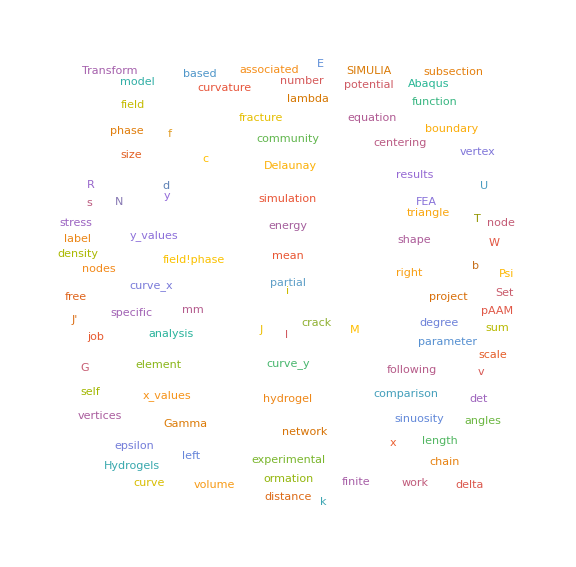

```mathematica
WordCloud[DeleteStopwords[webpage], ImageSize->Large]
```

```mathematica
contents=TextContents[webpage,VerifyInterpretation->True]
```

Dataset[<>]

```mathematica
counts=ReverseSort@CountsBy[contents,#Type&]
```

### Source Code

```mathematica
Options[KeywordsGraph]={DirectedEdges->False,EdgeWeight->Automatic,"LowerCase"->True,"StopWords"->True,VertexLabels->Automatic,VertexWeight->Automatic};

KeywordsGraph[text_String,number_Integer?Positive,blist_List:{},rlist_List:{},opts:OptionsPattern[{KeywordsGraph,Graph}]]:=Module[{keycounts,keywords,edges,edgeCount,data=Replace[DeleteCases[TextWords[If[TrueQ[OptionValue["StopWords"]],DeleteStopwords,Identity][If[TrueQ[OptionValue["LowerCase"]],ToLowerCase,Identity][text]]],Alternatives@@blist],rlist,{1}]},keycounts=Counts[data];Quiet[Check[keywords=TakeLargest[keycounts,number],Return[Failure["KeywordCount",<|"MessageTemplate"->"Number of specified keywords `1` exceeds the actual number of keywords `2`.","MessageParameters"->{number,Length[keycounts]}|>],Module]]];edges=Partition[Cases[data,Alternatives@@Keys[keywords]],2,1];edgeCount=If[TrueQ[Replace[OptionValue[DirectedEdges],Automatic:>False]],KeySelect[Counts[DirectedEdge@@@edges],#[[1]]!=#[[2]]&],KeySelect[Counts[Sort/@UndirectedEdge@@@edges],#[[1]]!=#[[2]]&]];Graph[Keys[keywords],Keys[edgeCount],FilterRules[Flatten[Join[{opts,VertexWeight->Replace[OptionValue[VertexWeight],Automatic:>Values[keywords]],EdgeWeight->Replace[OptionValue[EdgeWeight],Automatic:>Values[edgeCount]]},Options[KeywordsGraph]]],Options[Graph]]]]
```

### Graph Plot

```mathematica
CommunityGraphPlot[KeywordsGraph[DeleteStopwords[webpage],150,VertexSize->"VertexWeight",VertexStyle->Directive[Blue],EdgeStyle->Directive[Black,Dashed,Opacity[0.05]]],CommunityBoundaryStyle->Directive[Red,Dashed,Opacity[1]],ImageSize->Full,GraphLayout->"RadialEmbedding",BaseStyle->{FontSize->18}]
```

-Graphics-